# Elongation of network

### Definition of generation

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

### Program

```mathematica
cyclomaticComolexity[{eCount_,nCount_,wcgCount_}]:=eCount-nCount+2wcgCount
```

### count of published articles (1971 ~ 2023, 1950 ~ 2020)

```mathematica
pubyearTlySort["whole"]=Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearCount.wl"];
```

登録論文数 （出版年）

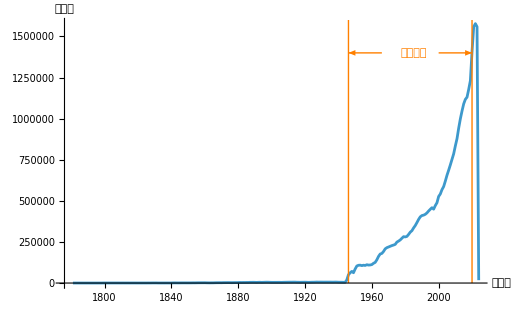

```mathematica
ListPlot[ToExpression[pubyearTlySort["whole"]],Joined->True,PlotRange->All,AxesLabel->{"出版年","収録数"},Epilog->{Orange,Line[{{1946,0},{1946,1.6 10^6}}],Line[{{2020,0},{2020,1.6 10^6}}],Arrow[{{1946+20,1.4 10^6},{1946,1.4 10^6}}],Arrow[{{2020-20,1.4 10^6},{2020,1.4 10^6}}],Text[Style["対象範囲"],{1985,1.4 10^6}]}]
```

```mathematica
(pubyearTlySort[1946,2020]=Cases[pubyearTlySort["whole"],x_/;ToExpression[x[[1]]]<=2020&&ToExpression[x[[1]]]>=1946])//Length
```

75

```mathematica
artcountByyear=Map[Total,Map[#[[2]]&,Partition[pubyearTlySort[1946,2020],5],{2}]]
```

{331362,534892,549642,725868,1014763,1166703,1352292,1542151,1917765,2144518,2393705,2971542,3776593,4954484,6064352}

```mathematica
cumulativeArtcount=Accumulate[artcountByyear]
```

{331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}

### count of lone node (no-ref, no-cited, not WCG) (1950 ~ 2020)

```mathematica
loneArtFiles=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle*wl"]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1950.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1955.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1960.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1965.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1970.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1975.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1980.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1985.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1990.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1995.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2000.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2005.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2010.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2015.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2020.wl}

```mathematica
loneArticles=Map[Get,loneArtFiles];
```

```mathematica
loneArtCount=Map[Length,loneArticles]
```

{296336,774662,1203519,1774556,2542940,3356424,4248958,5222321,6403037,7594669,9000206,10294609,10857321,11071404,11229183}

### basic graph properties (1950 ~ 2020)

```mathematica
wcgprofiles=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/*_wcgproperty.save"]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_wcgproperty.save}

```mathematica
Map[Get,wcgprofiles]//Length
```

15

Total vertex

```mathematica
totalV=Map[vctotal[#]&,gen]
```

{25659,106865,230664,387646,635815,991194,1452803,2022734,2761367,3715190,4704818,6388248,9604916,14351433,20271870}

```mathematica
grandtotalV=totalV+loneArtCount
```

{321995,881527,1434183,2162202,3178755,4347618,5701761,7245055,9164404,11309859,13705024,16682857,20462237,25422837,31501053}

```mathematica
loneArtPercent=loneArtCount/grandtotalV*100//N
```

{92.0312,87.8773,83.9167,82.0717,79.998,77.2014,74.5201,72.0812,69.8686,67.1509,65.6709,61.7077,53.0603,43.5491,35.647}

Total edge

```mathematica
totalE=Map[Total[ec[#]]&,gen]
```

{33832,182387,474042,919064,1737693,3107381,5106059,7927708,11950422,17666111,23761602,33378392,61234426,124935745,223840771}

WCG count

```mathematica
wcgN=Map[wcgcount[#]&,gen]
```

{2353,3851,4624,5729,7020,8446,9401,10026,10687,11361,12147,13000,13398,13643,14933}

Max WCG vertex count

```mathematica
wcgVmax=Map[vcmax[#]&,gen]
```

{17910,94830,216474,370660,615244,966113,1425267,1993398,2730892,3683220,4670358,6351561,9568400,14315982,20235562}

Max WCG vertex count %

```mathematica
wcgVmaxperc=Round[Map[vcmax[#]&,gen]/Map[vctotal[#]&,gen]*100//N,0.1]
```

{69.8,88.7,93.8,95.6,96.8,97.5,98.1,98.5,98.9,99.1,99.3,99.4,99.6,99.8,99.8}

Max WCG vertex count % (from all articles)

```mathematica
wcgVmaxpercAll=Round[Map[vcmax[#]&,gen]/cumulativeArtcount*100//N,0.1]
```

{5.4,10.9,15.3,17.3,19.5,22.3,25.1,27.6,29.9,32.7,34.2,38.2,46.9,56.4,64.4}

Cyclomatic Complexity

```mathematica
cyclomaticTri={totalE,totalV,wcgN}//Transpose
```

{{33832,25659,2353},{182387,106865,3851},{474042,230664,4624},{919064,387646,5729},{1737693,635815,7020},{3107381,991194,8446},{5106059,1452803,9401},{7927708,2022734,10026},{11950422,2761367,10687},{17666111,3715190,11361},{23761602,4704818,12147},{33378392,6388248,13000},{61234426,9604916,13398},{124935745,14351433,13643},{223840771,20271870,14933}}

```mathematica
complexity=Map[cyclomaticComolexity,cyclomaticTri]
```

{12879,83224,252626,542876,1115918,2133079,3672058,5925026,9210429,13973643,19081078,27016144,51656306,110611598,203598767}

Zipf' s "a"

```mathematica
zipfa=Round[Map[vcZipfParam[#][[2,2]]&,gen],0.01]
```

{7.51,11.26,12.1,13.4,13.94,13.13,13.7,14.18,14.7,15.4,15.4,17.27,17.87,18.64,19.1}

Table

```mathematica
wcgtblhead={"Generation","WCG","WCG vertices","WCG edges","Lone vertices","Largest WCG vertices","Largest WCG vertices %","Largest WCG vertices % (all articles)","complexity","Zipf's a"}
```

{Generation,WCG,WCG vertices,WCG edges,Lone vertices,Largest WCG vertices,Largest WCG vertices %,Largest WCG vertices % (all articles),complexity,Zipf's a}

```mathematica
wcgtblheadJ={"累積世代","WCG数","連結ノード総数","エッジ総数","孤立ノード数","最大WCGノード数","最大WCGノード %","最大WCGノード % (孤立ノード含)","複雑性","Zipfの係数a"}
```

{累積世代,WCG数,連結ノード総数,エッジ総数,孤立ノード数,最大WCGノード数,最大WCGノード %,最大WCGノード % (孤立ノード含),複雑性,Zipfの係数a}

```mathematica
wcgtblval={wcgN,totalV,totalE,loneArtCount,wcgVmax,wcgVmaxperc,wcgVmaxpercAll,complexity,zipfa}
```

{{2353,3851,4624,5729,7020,8446,9401,10026,10687,11361,12147,13000,13398,13643,14933},{25659,106865,230664,387646,635815,991194,1452803,2022734,2761367,3715190,4704818,6388248,9604916,14351433,20271870},{33832,182387,474042,919064,1737693,3107381,5106059,7927708,11950422,17666111,23761602,33378392,61234426,124935745,223840771},{296336,774662,1203519,1774556,2542940,3356424,4248958,5222321,6403037,7594669,9000206,10294609,10857321,11071404,11229183},{17910,94830,216474,370660,615244,966113,1425267,1993398,2730892,3683220,4670358,6351561,9568400,14315982,20235562},{69.8,88.7,93.8,95.6,96.8,97.5,98.1,98.5,98.9,99.1,99.3,99.4,99.6,99.8,99.8},{5.4,10.9,15.3,17.3,19.5,22.3,25.1,27.6,29.9,32.7,34.2,38.2,46.9,56.4,64.4},{12879,83224,252626,542876,1115918,2133079,3672058,5925026,9210429,13973643,19081078,27016144,51656306,110611598,203598767},{7.51,11.26,12.1,13.4,13.94,13.13,13.7,14.18,14.7,15.4,15.4,17.27,17.87,18.64,19.1}}

累積世代ごとのレファレンスネットワークの属性:

論文数、WCG数、最大WCGにおける論文数（そのパーセンテージ）、すべての論文を対象にした場合の最大WCGにおける論文数のパーセンテージ、WCGを構成する論文数におけるZipfの係数a（孤立ノードを含まない）。

```mathematica
(wcgtblJ=Prepend[Transpose[{gen,wcgN,totalV,totalE,loneArtCount,wcgVmax,wcgVmaxperc,wcgVmaxpercAll,complexity,zipfa}],wcgtblheadJ])//TableForm
```

累積世代 | WCG数 | 連結ノード総数 | エッジ総数 | 孤立ノード数 | 最大WCGノード数 | 最大WCGノード % | 最大WCGノード % (孤立ノード含) | 複雑性 | Zipfの係数a
1946-1950 | 2353 | 25659 | 33832 | 296336 | 17910 | 69.8 | 5.4 | 12879 | 7.51
1946-1955 | 3851 | 106865 | 182387 | 774662 | 94830 | 88.7 | 10.9 | 83224 | 11.26
1946-1960 | 4624 | 230664 | 474042 | 1203519 | 216474 | 93.8 | 15.3 | 252626 | 12.1
1946-1965 | 5729 | 387646 | 919064 | 1774556 | 370660 | 95.6 | 17.3 | 542876 | 13.4
1946-1970 | 7020 | 635815 | 1737693 | 2542940 | 615244 | 96.8 | 19.5 | 1115918 | 13.94
1946-1975 | 8446 | 991194 | 3107381 | 3356424 | 966113 | 97.5 | 22.3 | 2133079 | 13.13
1946-1980 | 9401 | 1452803 | 5106059 | 4248958 | 1425267 | 98.1 | 25.1 | 3672058 | 13.7
1946-1985 | 10026 | 2022734 | 7927708 | 5222321 | 1993398 | 98.5 | 27.6 | 5925026 | 14.18
1946-1990 | 10687 | 2761367 | 11950422 | 6403037 | 2730892 | 98.9 | 29.9 | 9210429 | 14.7
1946-1995 | 11361 | 3715190 | 17666111 | 7594669 | 3683220 | 99.1 | 32.7 | 13973643 | 15.4
1946-2000 | 12147 | 4704818 | 23761602 | 9000206 | 4670358 | 99.3 | 34.2 | 19081078 | 15.4
1946-2005 | 13000 | 6388248 | 33378392 | 10294609 | 6351561 | 99.4 | 38.2 | 27016144 | 17.27
1946-2010 | 13398 | 9604916 | 61234426 | 10857321 | 9568400 | 99.6 | 46.9 | 51656306 | 17.87
1946-2015 | 13643 | 14351433 | 124935745 | 11071404 | 14315982 | 99.8 | 56.4 | 110611598 | 18.64
1946-2020 | 14933 | 20271870 | 223840771 | 11229183 | 20235562 | 99.8 | 64.4 | 203598767 | 19.1

```mathematica
wcgpltheadJ={"累積世代","WCG数","連結ノード\n総数","エッジ\n総数","孤立\nノード数","最大WCG\nノード数","複雑性"}
```

{累積世代,WCG数,連結ノード
総数,エッジ
総数,孤立
ノード数,最大WCG
ノード数,複雑性}

```mathematica
ListPlot[{gen,wcgN,totalV,totalE,loneArtCount,wcgVmax,complexity},Joined->True,PlotRange->Full,Ticks->{genticks,Automatic},PlotLabels->wcgpltheadJ,AxesLabel->{"累積世代","カウント"}]
```

-Graphics-

```mathematica
percentHead={"最大WCGノード %","最大WCGノード % \n(分母に孤立ノード含む)","孤立ノード %"}
```

{最大WCGノード %,最大WCGノード % 
(分母に孤立ノード含む),孤立ノード %}

```mathematica
ListPlot[{wcgVmaxpercAll,loneArtCount/(totalV+loneArtCount)*100,wcgVmaxperc},Joined->True,PlotRange->Full,Ticks->{genticks,Automatic},AxesLabel->{"累積世代","%"},PlotLabels->{"最大WCG\nノード","孤立ノード","最大WCGノード\n/総WCGノード"}]
```

-Graphics-

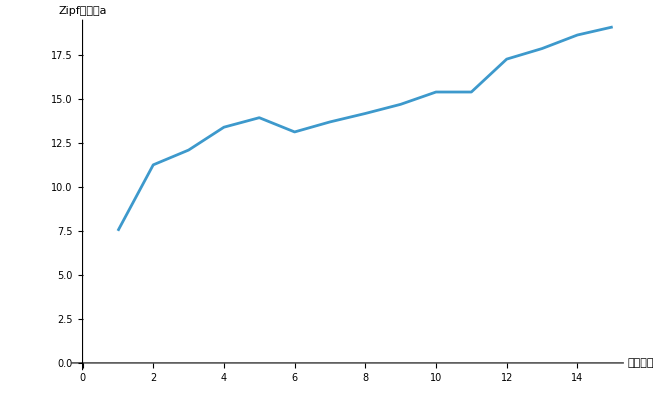

```mathematica
ListPlot[zipfa,AxesLabel->{"累積世代","Zipfの係数a"},Joined->True]
```

### graph elongation (1950 ~ 2020)

#### Table

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/graphDiff.save"];
```

A. 新規に発生した引用数*

```mathematica
newedgecountAll=Table[newedgecount[n],{n,1955,2020,5}]
```

{148555,291655,445022,818629,1369688,1998678,2821649,4022714,5715688,6095490,9616785,27854672,63696093,98878679}

B-3 新規に発生した引用のうちtop1%論文に対する引用数

```mathematica
newedgecounttop1percAll=Table[newedgecounttop1perc[n],{n,1955,2020,5}]
```

{304,1235,2835,9219,14013,17085,26144,50019,45096,30524,21803,44967,268426,676422}

```mathematica
newedgecounttop1percAllratio=Round[newedgecounttop1percAll/newedgecountAll//N,0.001]*100
```

{0.2,0.4,0.6,1.1,1.,0.9,0.9,1.2,0.8,0.5,0.2,0.2,0.4,0.7}

```mathematica
newedgecounttop1percAlltbl=Table[ToString[newedgecounttop1percAll[[n]]]<>" ("<>ToString[newedgecounttop1percAllratio[[n]]]<>")",{n,14}]
```

{304 (0.2),1235 (0.4),2835 (0.6),9219 (1.1),14013 (1.),17085 (0.9),26144 (0.9),50019 (1.2),45096 (0.8),30524 (0.5),21803 (0.2),44967 (0.2),268426 (0.4),676422 (0.7)}

A - 1. 新規に発生した引用により結合が発生した前世代WCG数*

```mathematica
newconnectedWCGcountAll=Table[newconnectedWCGcount[n],{n,1955,2020,5}]
```

{1280,1485,1297,1411,1549,1716,1683,1553,1450,1147,1508,2576,3404,3472}

A-3. 新規に発生した引用に関して異なる前世代WCGを結合する論文の数*

```mathematica
newMetaconnectedArtcountAll=Table[newMetaconnectedArtcount[n],{n,1955,2020,5}]
```

{1632,1942,1717,1937,2240,2520,2480,2438,2345,1603,2553,6243,11124,11676}

A-4. 結合後のWCG数*

```mathematica
newMetaconnectedWCGcountAll=Table[newMetaconnectedWCGcount[n],{n,1955,2020,5}]
```

{909,1185,1070,1133,1306,1500,1478,1392,1310,1048,1353,2407,3235,3255}

WCGの結合率*

```mathematica
WCGconnectedRatio=Round[1-(newMetaconnectedWCGcountAll/wcgN[[;;-2]])//N,0.01]
```

{0.61,0.69,0.77,0.8,0.81,0.82,0.84,0.86,0.88,0.91,0.89,0.81,0.76,0.76}

```mathematica
WCGcongen=Table[n,{n,1955,2020,5}]
```

{1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
elgTblHead={"累積世代","新規に発生した引用数","新規に発生した引用のうち\n前世代主要論文に対する引用(%)","新規に発生した引用のうち\n異なる前世代WCGを結合する論文の数","新規に発生した引用により\n結合が発生した前世代WCG数","結合後のWCG数","前世代WCG数","WCGの結合効率"}
```

{累積世代,新規に発生した引用数,新規に発生した引用のうち
前世代主要論文に対する引用(%),新規に発生した引用のうち
異なる前世代WCGを結合する論文の数,新規に発生した引用により
結合が発生した前世代WCG数,結合後のWCG数,前世代WCG数,WCGの結合効率}

```mathematica
Prepend[Transpose[{WCGcongen,newedgecountAll,newedgecounttop1percAlltbl,newMetaconnectedArtcountAll,newconnectedWCGcountAll,newMetaconnectedWCGcountAll,wcgN[[;;-2]],WCGconnectedRatio}],elgTblHead]//TableForm
```

累積世代 | 新規に発生した引用数 | 新規に発生した引用のうち
前世代主要論文に対する引用(%) | 新規に発生した引用のうち
異なる前世代WCGを結合する論文の数 | 新規に発生した引用により
結合が発生した前世代WCG数 | 結合後のWCG数 | 前世代WCG数 | WCGの結合効率
1955 | 148555 | 304 (0.2) | 1632 | 1280 | 909 | 2353 | 0.61
1960 | 291655 | 1235 (0.4) | 1942 | 1485 | 1185 | 3851 | 0.69
1965 | 445022 | 2835 (0.6) | 1717 | 1297 | 1070 | 4624 | 0.77
1970 | 818629 | 9219 (1.1) | 1937 | 1411 | 1133 | 5729 | 0.8
1975 | 1369688 | 14013 (1.) | 2240 | 1549 | 1306 | 7020 | 0.81
1980 | 1998678 | 17085 (0.9) | 2520 | 1716 | 1500 | 8446 | 0.82
1985 | 2821649 | 26144 (0.9) | 2480 | 1683 | 1478 | 9401 | 0.84
1990 | 4022714 | 50019 (1.2) | 2438 | 1553 | 1392 | 10026 | 0.86
1995 | 5715688 | 45096 (0.8) | 2345 | 1450 | 1310 | 10687 | 0.88
2000 | 6095490 | 30524 (0.5) | 1603 | 1147 | 1048 | 11361 | 0.91
2005 | 9616785 | 21803 (0.2) | 2553 | 1508 | 1353 | 12147 | 0.89
2010 | 27854672 | 44967 (0.2) | 6243 | 2576 | 2407 | 13000 | 0.81
2015 | 63696093 | 268426 (0.4) | 11124 | 3404 | 3235 | 13398 | 0.76
2020 | 98878679 | 676422 (0.7) | 11676 | 3472 | 3255 | 13643 | 0.76

#### Visualization

```mathematica
withG[currentList_List,currentG_Integer]:=Module[{len,prevG},
prevG=currentG-5;
len=Length[currentList];
Table[Map[prevG[#]->currentG[n]&,currentList[[n]]],{n,len}]
]
```

```mathematica
WCGlinkwithG[currentList_List,currentG_Integer]:=Tally[Flatten[withG[currentList,currentG]]]
```

```mathematica
WCGlinkToGraph[link_]:=Graph[Map[DirectedEdge[#[[1,1]],#[[1,2]],#[[2]]]&,link]]
```

```mathematica
refdatadir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/

```mathematica
datafile="elongationMat.save"
```

elongationMat.save

```mathematica
Do[WCGcount[genEnd[[n]]]=wcgN[[n]],{n,1,15}]
```

```mathematica
wcgsavefile="WCGELinkAll.save"
```

WCGELinkAll.save

```mathematica
Get[refdatadir<>wcgsavefile];
```

: Visualization : count : all -> 表示に時間がかかるのでやめる。

: Visualization : count >= 10

```mathematica
WCGElink[10]=Cases[WCGElink["All"],x_/;x[[2]]>=10];
```

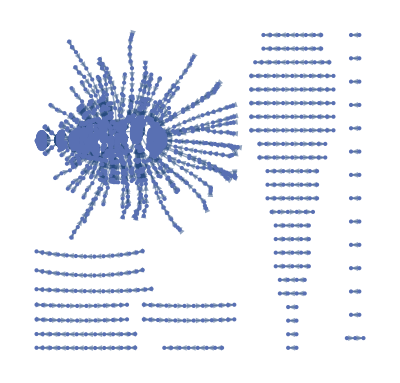

```mathematica
WCGelgraph[10]=WCGlinkToGraph[WCGElink[10]]
```

```mathematica
vc10=Map[#->{#[[0]],#[[1]]/WCGcount[#[[0]]]*100}&,WCGelgraph[10]//VertexList];
```

```mathematica
max=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Max
min=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Min
```

1.99873×10^8

10.

```mathematica
myColors={Red,RGBColor[1,0.5,0],RGBColor[0.9,0.8,0],RGBColor[0.3,0.6,1]}
```

{RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0.9, 0.8, 0],RGBColor[0.3, 0.6, 1]}

```mathematica
myColorData[v_]:=Which[v>=45,Red,45>v&&v>=25,RGBColor[1,0.5,0],25>v&&v>=15,RGBColor[0.9,0.8,0], 15>v&&v>=10,RGBColor[0.3,0.6,1]]
```

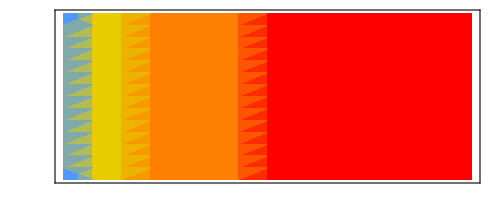
-Graphics-
弱    <-結合->    強

```mathematica
colorscale=Grid[{{DensityPlot[x,{x,min,80},{y,0,10},ColorFunction->myColorData,ColorFunctionScaling->False,AspectRatio->Automatic,FrameTicks->{{None,None},{None,None}}]},{"弱    <-結合->    強"}}]
```

```mathematica
es=Table[EdgeList[WCGelgraph[10]][[n]]->myColorData[(EdgeList[WCGelgraph[10]][[n]][[3]])],{n,Length[EdgeList[WCGelgraph[10]]]}]
```

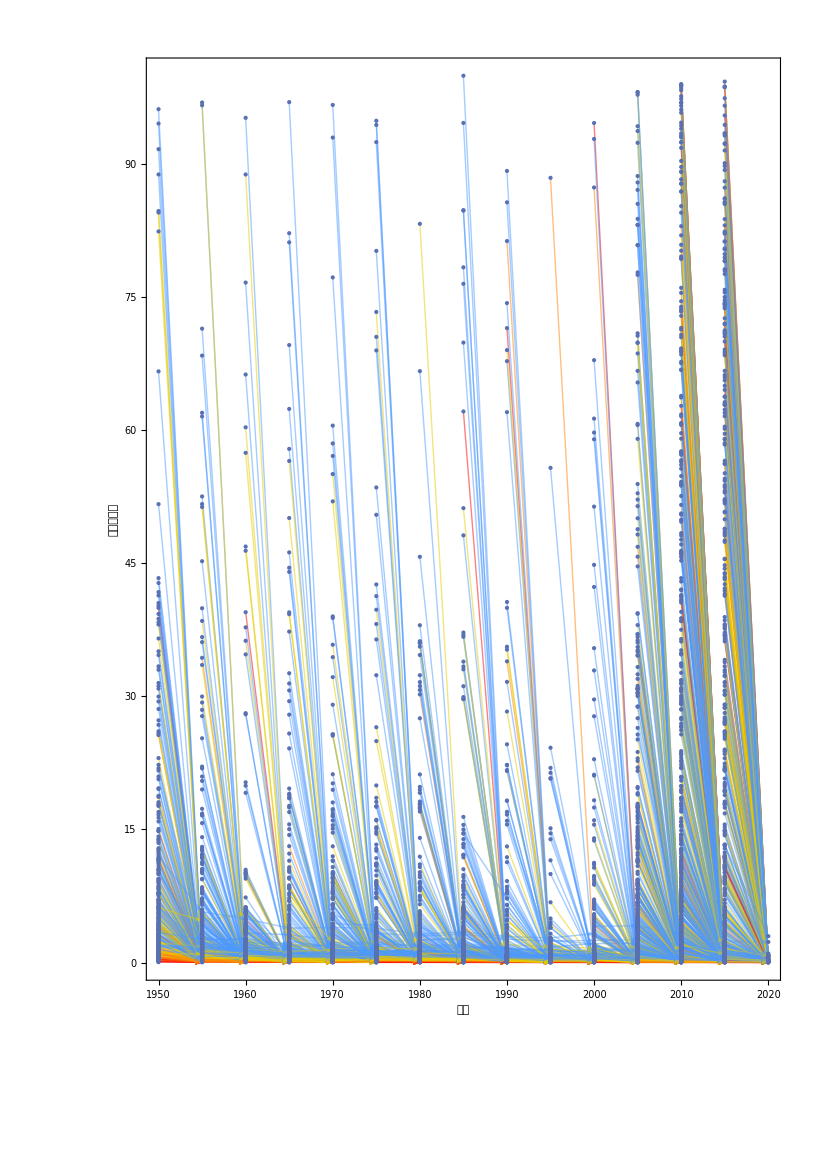

```mathematica
gp10=GraphPlot[Graph[WCGelgraph[10],VertexCoordinates->vc10,EdgeStyle->es,Frame->True,FrameTicks->{Automatic,Automatic}],FrameLabel->{"世代","順位百分率"}]
```

Edge proportion

```mathematica
epTbl=Table[Counts[Map[#[[2]]&,Cases[es,x_/;Head[x[[1,1]]]==(n-5)&&Head[x[[1,2]]]==n]]],{n,1955,2020,5}]
```

{<|RGBColor[0.9, 0.8, 0]→72,RGBColor[1, 0, 0]→13,RGBColor[0.3, 0.6, 1]→115,RGBColor[1, 0.5, 0]→27|>,<|RGBColor[1, 0, 0]→4,RGBColor[0.3, 0.6, 1]→127,RGBColor[0.9, 0.8, 0]→59,RGBColor[1, 0.5, 0]→18|>,<|RGBColor[1, 0, 0]→5,RGBColor[0.3, 0.6, 1]→103,RGBColor[0.9, 0.8, 0]→59,RGBColor[1, 0.5, 0]→10|>,<|RGBColor[1, 0, 0]→4,RGBColor[0.3, 0.6, 1]→114,RGBColor[1, 0.5, 0]→11,RGBColor[0.9, 0.8, 0]→61|>,<|RGBColor[1, 0, 0]→3,RGBColor[0.9, 0.8, 0]→75,RGBColor[0.3, 0.6, 1]→128,RGBColor[1, 0.5, 0]→13|>,<|RGBColor[1, 0, 0]→8,RGBColor[0.3, 0.6, 1]→136,RGBColor[0.9, 0.8, 0]→66,RGBColor[1, 0.5, 0]→24|>,<|RGBColor[1, 0, 0]→8,RGBColor[0.3, 0.6, 1]→131,RGBColor[1, 0.5, 0]→21,RGBColor[0.9, 0.8, 0]→71|>,<|RGBColor[1, 0, 0]→11,RGBColor[0.3, 0.6, 1]→148,RGBColor[0.9, 0.8, 0]→70,RGBColor[1, 0.5, 0]→24|>,<|RGBColor[1, 0, 0]→7,RGBColor[0.9, 0.8, 0]→62,RGBColor[0.3, 0.6, 1]→123,RGBColor[1, 0.5, 0]→13|>,<|RGBColor[1, 0, 0]→4,RGBColor[0.3, 0.6, 1]→102,RGBColor[0.9, 0.8, 0]→51,RGBColor[1, 0.5, 0]→9|>,<|RGBColor[1, 0, 0]→10,RGBColor[0.9, 0.8, 0]→71,RGBColor[1, 0.5, 0]→13,RGBColor[0.3, 0.6, 1]→138|>,<|RGBColor[1, 0, 0]→11,RGBColor[0.9, 0.8, 0]→125,RGBColor[1, 0.5, 0]→36,RGBColor[0.3, 0.6, 1]→238|>,<|RGBColor[1, 0, 0]→28,RGBColor[0.3, 0.6, 1]→289,RGBColor[1, 0.5, 0]→61,RGBColor[0.9, 0.8, 0]→163|>,<|RGBColor[1, 0, 0]→33,RGBColor[0.3, 0.6, 1]→227,RGBColor[1, 0.5, 0]→55,RGBColor[0.9, 0.8, 0]→137|>}

```mathematica
myColors
```

{RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0.9, 0.8, 0],RGBColor[0.3, 0.6, 1]}

```mathematica
colorPerc[asc_]:=Module[{total},
total=Total[asc];
Map[asc,myColors]/total
]
```

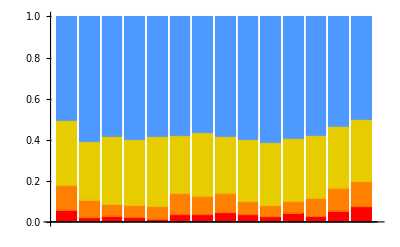

```mathematica
BarChart[Map[colorPerc,epTbl],ChartLayout->"Stacked",ChartStyle->myColors]
```